###### m = 2 ######

λ = 1.36165

3/(3+4.08496 s+1.8541 s^2)

1.61803/(1.61803+2.2032 s+1. s^2)

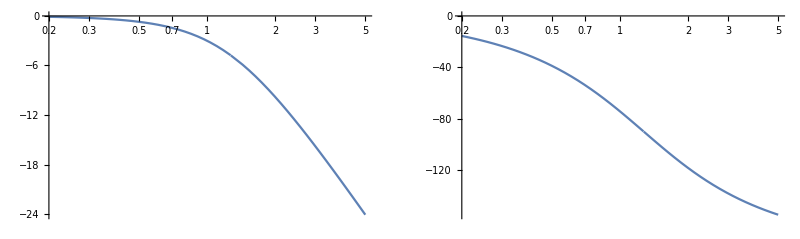

###### m = 3 ######

λ = 1.75567

15/(15+26.3351 s+18.4943 s^2+5.41166 s^3)

2.77179/((1.32268+1. s) (2.0956+2.09482 s+1. s^2))

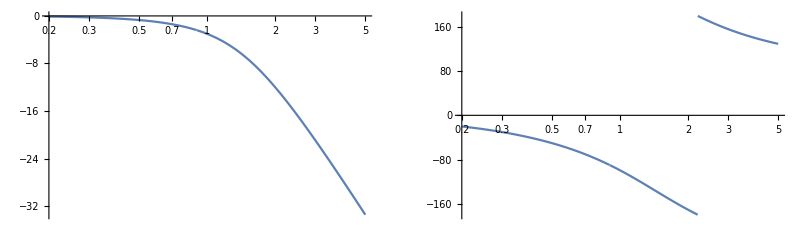

###### m = 4 ######

λ = 2.11392

105/(105+221.961 s+201.089 s^2+94.4635 s^3+19.9688 s^4)

5.2582/((2.57076+1.99042 s+1. s^2) (2.04539+2.74014 s+1. s^2))

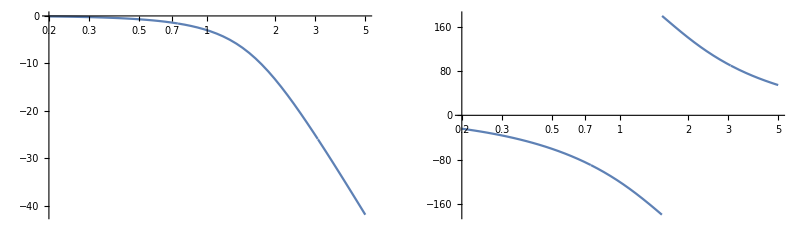

###### m = 5 ######

λ = 2.42741

945/(945+2293.9 s+2474.78 s^2+1501.82 s^3+520.792 s^4+84.2784 s^5)

11.2128/((1.50232+1. s) (3.08135+1.91535 s+1. s^2) (2.42222+2.76175 s+1. s^2))

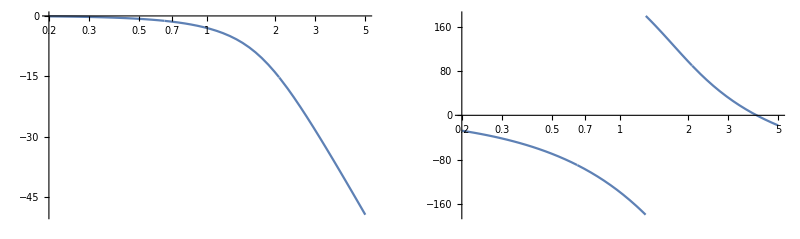

###### m = 6 ######

λ = 2.7034

10395/(10395+28101.8 s+34531.9 s^2+24894.3 s^3+11216.5 s^4+3032.26 s^5+390.353 s^6)

26.6298/((3.62791+1.86131 s+1. s^2) (2.85329+2.76372 s+1. s^2) (2.57256+3.14298 s+1. s^2))

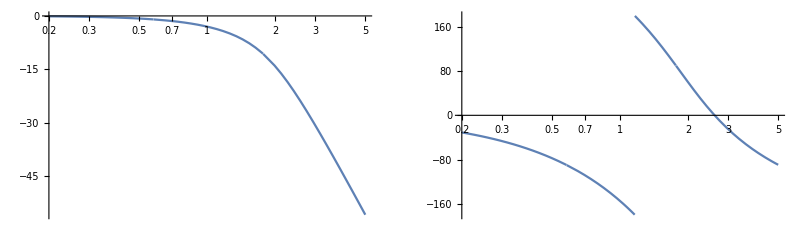

###### m = 7 ######

λ = 2.95172

135135/(135135+398881. s+543409. s^2+445553. s^3+239118. s^4+84697.2 s^5+18518.7 s^6+1952.22 s^7)

69.2213/((1.68437+1. s) (4.20041+1.81974 s+1. s^2) (3.32121+2.75781 s+1. s^2) (2.94588+3.22408 s+1. s^2))

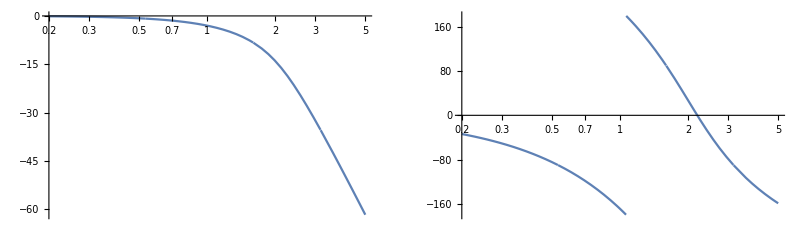

###### m = 8 ######

λ = 3.17962

2027025/(2027025+6.44516×10^6 s+9.56347×10^6 s^2+8.68805×10^6 s^3+5.31244×10^6 s^4+2.2522×10^6 s^5+651013. s^6+118284. s^7+10447.2 s^8)

194.026/((4.79052+1.78574 s+1. s^2) (3.81497+2.74768 s+1. s^2) (3.35656+3.27388 s+1. s^2) (3.16294+3.51482 s+1. s^2))

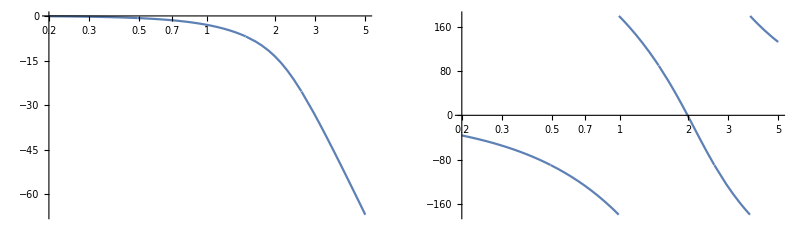

```mathematica
-Graphics-;
For[m=2,m≤8,m++,
rbsl[x_,m_]:=((2m-x)!)/(2^(m-x)x!(m-x)!);
Hbsl[s_,m_]:=rbsl[0,m]/(∑_(k=0)^m (rbsl[k,m] s^k));
λ=λ/.FindRoot[Abs[Hbsl[ⅈ λ,m]]==(√2)/2,{λ,1}];
Print["###### m = ",m," ######"];
Print["λ = ",λ];
Print[Hbsl[λ s,m]];
Print[Factor[Hbsl[λ s,m]]];
GraphicsRow[{LogLinearPlot[20 Log10[Abs[Hbsl[ⅈ ω λ,m]]],{ω,0.2,5}],
LogLinearPlot[180/π*Arg[Hbsl[ⅈ ω λ,m]],{ω,0.2,5}]}]//Print]
```

```mathematica
Factor[10395/(10395+28101.791661204366 s+34531.92944902424 s^2+24894.25267367996 s^3+11216.49995506067 s^4+3032.2630582493807 s^5+390.3526179018782 s^6)]
```

26.6298/((3.62791+1.86131 s+1. s^2) (2.85329+2.76372 s+1. s^2) (2.57256+3.14298 s+1. s^2))